```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
Δ=2Pi delt;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi Range[-.2,.2,0.0001]*10^9;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/2]*2.537717 10^-29;
d42=Sqrt[1/2]*2.537717 10^-29;
d31=Sqrt[1/2]*2.537717 10^-29;
d41=Sqrt[1/2]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4ⅈ d42^2 Nat (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ))/(e0 (omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ); 
χ32=(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ))/(e0 (omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{omegac1,omegac2
},
Transpose[{(δ/(2Pi))/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
χ42=(4ⅈ d42^2 Nat (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ))/(e0 (omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=(4 ⅈ d32^2 Nat (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ))/(e0 (omegac1^2 (w43-ⅈ (γ32+γ42+2 ⅈ δ+2 ⅈ Δ))+4 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
Δ=2Pi delt;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi Range[-0.05,0.05,0.00027]*10^9;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/2]*2.537717 10^-29;
d42=Sqrt[1/2]*2.537717 10^-29;
d31=Sqrt[1/2]*2.537717 10^-29;
d41=Sqrt[1/2]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{(δ/(2Pi))/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]]}],
Transpose[{(δ/(2Pi))/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]]}]
},
Transpose[{(δ/(2Pi))/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

Δ=2Pi delt;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi Range[-0.05,0.05,0.00027]*10^9;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/2]*2.537717 10^-29;
d42=Sqrt[1/2]*2.537717 10^-29;
d31=Sqrt[1/2]*2.537717 10^-29;
d41=Sqrt[1/2]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6) ;
u=Rbpress[T][[4]]; 



Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{(δ/(2Pi))/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
list=Table[{Table[δ,{i,1,4001}],Transpose[Lev4Test[50,15.865/1000,1/1000,0*10^6,δ*10^9,1]]}
,{δ,Range[-1,1,0.005]}];
testdata1=Flatten[Table[Transpose[{#2[[1]],#,#2[[2]]}&@@list[[i]]],{i,1,Length[Range[-1,1,0.005]]}],1];
func=Interpolation[testdata1];
img=ContourPlot[func[x,y],{x,-0.02,0.02},{y,-1,1},ImageSize->800,PlotPoints->200,PlotRange->{0,1},ClippingStyle->Automatic,GridLines->{{-2,-1,0,1,2},{-2,-1,0,1,2}},Method->{"GridLinesInFront"->True},FrameLabel->{Style["Two Photon Detuning δ (GHz)",20],Style["One Photon Detuning Δ (GHz)",20]},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.01,0,0.01,0.02},None}},FrameTicksStyle->Directive[40],PlotLegends->Placed[Automatic,Below],Contours->20



]
```

-Graphics-

```mathematica
Length[Range[-0.2,0.2,0.001]]
```

401

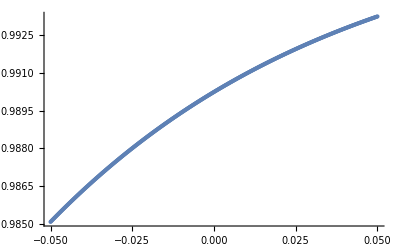

```mathematica
ListPlot[Lev4DoppTest[50,30/1000,1/1000,3*10^6,1*10^9,1]]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

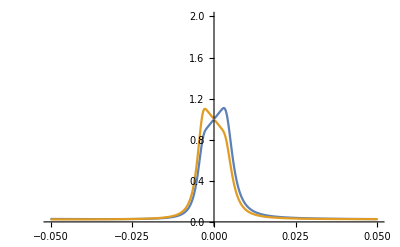

```mathematica
ListPlot[Lev4DoppTest[50,15.865/1000,1/1000,0*10^6,0*10^9,0,-61],PlotRange->{0,2},Joined->True]
```

```mathematica
[T_,P_,diam_,gam_,delt_,ab_,w_]
```

```mathematica
Lev3DoppTest[50,15.865/1000,1/1000,1.4*10^6,0*10^9,1]
```

Lev3DoppTest[50,0.015865,1/1000,1.4×10^6,0,1]

```mathematica
Manipulate[ListPlot[{Lev4DoppTest[50,15.865/1000,1/1000,γ*10^6,0*10^9,1,w],Lev3DoppTest[50,15.865/1000,1/1000,γ*10^6,0*10^9,1,w]},PlotRange->{0,1},Joined->True]
,{w,0,361},{γ,0,1.4}]
```

General::unfl: Underflow occurred in computation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

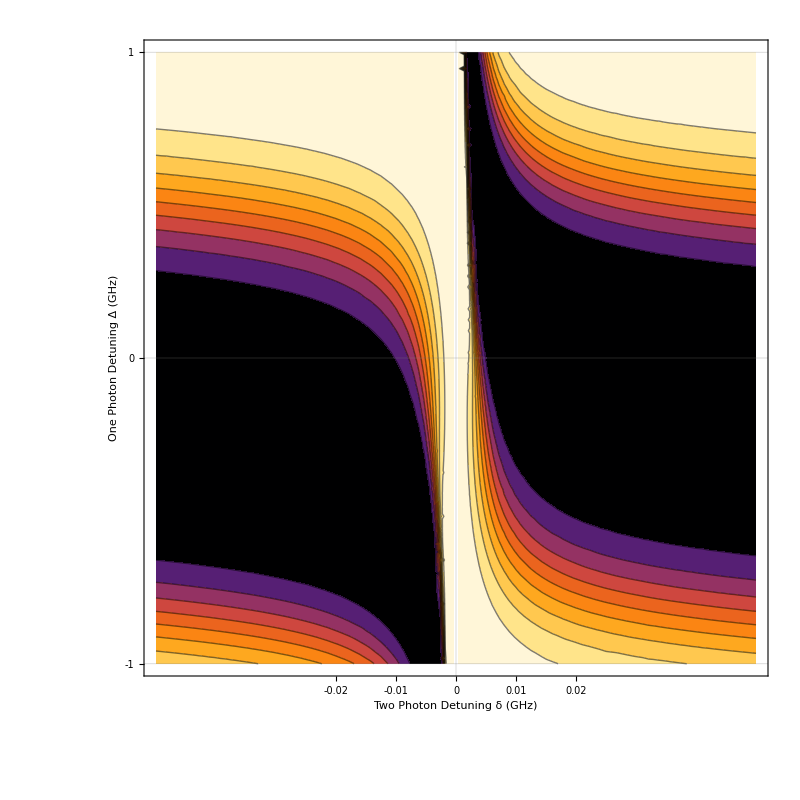

```mathematica
list=Table[{Table[δ,{i,1,501}],Transpose[Lev4DoppTest[50,15.865/1000,1/1000,0*10^6,δ*10^9,1]]}
,{δ,Range[-1,1,0.005]}];
testdata1=Flatten[Table[Transpose[{#2[[1]],#,#2[[2]]}&@@list[[i]]],{i,1,Length[Range[-1,1,0.005]]}],1];
func=Interpolation[testdata1];
img=ContourPlot[func[x,y],{x,-0.05,0.05},{y,-1,1},ImageSize->800,PlotRange->{0,1},ClippingStyle->Automatic,GridLines->{{-2,-1,0,1,2},{-2,-1,0,1,2}},Method->{"GridLinesInFront"->True},FrameLabel->{Style["Two Photon Detuning δ (GHz)",20],Style["One Photon Detuning Δ (GHz)",20]},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.01,0,0.01,0.02},None}},FrameTicksStyle->Directive[40],PlotLegends->Placed[Automatic,Below]



]
```

```mathematica
list=Table[{Table[δ,{i,1,4001}],Transpose[Lev4Test[50,15.865/1000,1/1000,0*10^6,δ*10^9,1]]}
,{δ,Range[-1,1,0.005]}];
testdata1=Flatten[Table[Transpose[{#2[[1]],#,#2[[2]]}&@@list[[i]]],{i,1,Length[Range[-1,1,0.005]]}],1];
func=Interpolation[testdata1];
img=ContourPlot[func[x,y],{x,-0.05,0.05},{y,-1,1},ImageSize->800,PlotPoints->200,PlotRange->{0,1},ClippingStyle->Automatic,GridLines->{{-2,-1,0,1,2},{-2,-1,0,1,2}},Method->{"GridLinesInFront"->True},FrameLabel->{Style["Two Photon Detuning δ (GHz)",20],Style["One Photon Detuning Δ (GHz)",20]},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.01,0,0.01,0.02},None}},FrameTicksStyle->Directive[40],PlotLegends->Placed[Automatic,Below],Contours->20



]
```

-Graphics-

```mathematica
list=Table[{Table[δ,{i,1,4001}],Transpose[Lev4Test[50,15.865/1000,1/1000,0*10^6,δ*10^9,1]]}
,{δ,Range[-1,1,0.005]}];
testdata1=Flatten[Table[Transpose[{#2[[1]],#,#2[[2]]}&@@list[[i]]],{i,1,Length[Range[-1,1,0.005]]}],1];
func=Interpolation[testdata1];
img=ContourPlot[func[x,y],{x,-0.05,0.05},{y,-1,1},ImageSize->800,PlotPoints->200,PlotRange->{0,1},ClippingStyle->Automatic,GridLines->{{-2,-1,0,1,2},{-2,-1,0,1,2}},Method->{"GridLinesInFront"->True},FrameLabel->{Style["Two Photon Detuning δ (GHz)",20],Style["One Photon Detuning Δ (GHz)",20]},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.01,0,0.01,0.02},None}},FrameTicksStyle->Directive[40],PlotLegends->Placed[Automatic,Below],Contours->20



]
```

-Graphics-

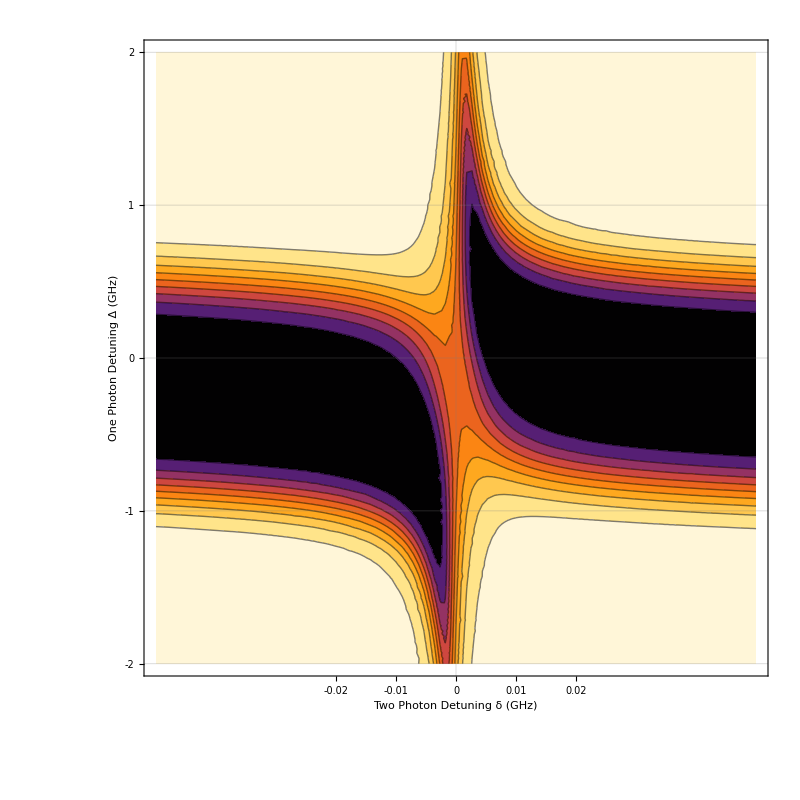

```mathematica
list=Table[{Table[δ,{i,1,501}],Transpose[Lev4DoppTest[50,15.865/1000,1/1000,1.4*10^6,δ*10^9,1]]}
,{δ,Range[-2,2,0.05]}];
testdata1=Flatten[Table[Transpose[{#2[[1]],#,#2[[2]]}&@@list[[i]]],{i,1,Length[Range[-2,2,0.05]]}],1];
func=Interpolation[testdata1];
img=ContourPlot[func[x,y],{x,-0.05,0.05},{y,-2,2},ImageSize->800,PlotRange->{0,1},ClippingStyle->Automatic,GridLines->{{-2,-1,0,1,2},{-2,-1,0,1,2}},Method->{"GridLinesInFront"->True},FrameLabel->{Style["Two Photon Detuning δ (GHz)",20],Style["One Photon Detuning Δ (GHz)",20]},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.01,0,0.01,0.02},None}},FrameTicksStyle->Directive[40],PlotLegends->Placed[Automatic,Below]



]
```